### Basic Examples

Retrieve the resource:

```mathematica
ResourceObject["Epidemic Data for Novel Coronavirus COVID-19"]
```

ResourceObject[…]

Retrieve the default content:

```mathematica
ResourceData["Epidemic Data for Novel Coronavirus COVID-19"]
```

Dataset[<>]

Latest update date:

```mathematica
ResourceData["Epidemic Data for Novel Coronavirus COVID-19"][Max,#ConfirmedCases["LastDate"]&]
```

Mon 24 Feb 2020 00:00:00GMT-6.

Color countries by the latest confirmed cases:

```mathematica
GeoRegionValuePlot[Normal@ResourceData["Epidemic Data for Novel Coronavirus COVID-19"][GroupBy["Country"],Total,#ConfirmedCases["LastValue"]&]]
```

-Graphics-

Create a bubble chart of the confirmed cases for the regions in China:

```mathematica
Manipulate[GeoBubbleChart[Normal@data[Select[MatchQ[Entity["Country","China"],#Country]&]][All,{#AdministrativeDivision,#ConfirmedCases[date]}&],BubbleSizes->({.01+#[[1]]/500,#[[2]]/60000}&@Normal@data[Select[MatchQ[Entity["Country","China"],#Country]&]][MinMax,#ConfirmedCases[date]&])],{{date,dates[[1]],Dynamic[date]},dates},ControlType->Slider,SynchronousInitialization->False,SynchronousUpdating->False,TrackedSymbols:>{date},Initialization:>{data=ResourceData["Epidemic Data for Novel Coronavirus COVID-19"];dates=Sort@Union@Flatten@Normal@data[All,#ConfirmedCases["DateList"]&]}]
```

-Graphics-

Plot estimated confirmed cases in the regions of China over the past few days:

```mathematica
cases=ResourceData["Epidemic Data for Novel Coronavirus COVID-19"][Select[MemberQ[{Entity["AdministrativeDivision",{"Hubei","China"}],Entity["AdministrativeDivision",{"Zhejiang","China"}],Entity["AdministrativeDivision",{"Guangdong","China"}]},#AdministrativeDivision]&]][All,{"AdministrativeDivision","ConfirmedCases"}];
```

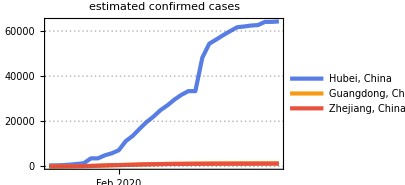
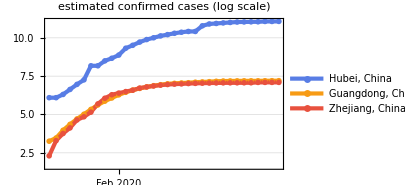

```mathematica
Row[{DateListPlot[Legended[#[[2]],#[[1]]]&/@cases,PlotTheme->"Business",PlotLabel->"estimated confirmed cases",ImageSize->300,PlotRange->Full],DateListLogPlot[Legended[#[[2]],#[[1]]]&/@cases,PlotTheme->"Business",PlotLabel->"estimated confirmed cases (log scale)",ImageSize->300,PlotRange->Full]}]
```